```mathematica
rx = 10.0*BohrinLi6vdw;
rf = 300*BohrinLi6vdw;
r0 = 40*BohrinLi6vdw;
rmin = 2.0*BohrinLi6vdw;
rmax = r0;
ltest = 0;
Etest = 10^-16; 
ksqrC6[Ε_,l_,r_]:=(Ε - Li6vlrC6[r]-(l(l+1))/r^2);
BC1C6[Ε_,l_,r_,rx_]:=1/Sqrt[(Ε - Li6vlrC6[r]-(l(l+1))/r^2)^(1/2)]/.r->rx;
BC2C6[Ε_,l_,r_,rx_]:=D[1/Sqrt[(Ε - Li6vlrC6[r]-(l(l+1))/r^2)^(1/2)],r]/.r->rx;
α0sol=Flatten[Table[NDSolve[{α''[r]+ksqrC6[Etest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1C6[Etest,ltest,r,rx],α'[rx]==BC2C6[Etest,ltest,r,rx]},α,{r,rx,rf}],{ltest,0,2}]];
α0fun=Table[α/.α0sol[[i]],{i,1,Length[α0sol]}];
nr=300;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(α0fun[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,2}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,2}];
phivals=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0fun[[ltest+1]],phaseintfun[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,2}],{rf,rGrid}]];
```

```mathematica
ϕLi6=Table[phivals[[i,nr,2]],{i,1,Length[phivals]}]
```

{0.337401,1.11013,-1.27159}

```mathematica
calcTanGammaC6[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{αfun,phaseint,g0,g0p,f0,f0p,αp,α,κ,rp,gbound,gboundp,tanγ},
αfun = NDSolveValue[{α''[r] + ksqrC6[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1C6[Ε,l,r,rx],α'[rx] == BC2C6[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
κ=√-Ε;
gbound=√(κ/π rp) BesselK[l+1/2,κ rp]/.rp->rf;
gboundp=D[√(κ/π rp) BesselK[l+1/2,κ rp],rp]/.rp->rf;
tanγ =-(gbound g0p-gboundp g0)/(gbound f0p - gboundp f0);
Return[tanγ]
]
```

```mathematica
gammaTableC6=Table[{-EGrid[[ii]],ArcTan[calcTanGammaC6[0,rx,rf,r,-EGrid[[ii]],ϕLi6[[1]]]]},{ii,1,Length[EGrid]}];
```

```mathematica
GammaTableC6new=gammaTableC6;
For[i=1,i<Length[gammaTableC6],i++,
If[(gammaTableC6[[i+1,2]]-gammaTableC6[[i,2]]<-1.2),Print[i];
GammaTableC6new[[i+1;;En,2]]=GammaTableC6new[[i+1;;En,2]]+π,GammaTableC6new[[i+1;;En,2]]=GammaTableC6new[[i+1;;En,2]]]
]
```

316

```mathematica
Fit[Table[{GammaTableC6new[[ii,1]]*-1,GammaTableC6new[[ii,2]]},{ii,1,Length[GammaTableC6new]}],{ϵ^(1/2),ϵ,ϵ^(3/2),ϵ^2},ϵ]
```

```mathematica
GammaC6[ϵ_]:=0.44450838598046727 √-ϵ+0.042506261502103244 ϵ+0.003964874711287541 (-ϵ)^(3/2)-0.0001523583044042683 ϵ^2
```

```mathematica
GammaC6fun = Interpolation[GammaTableC6new(*,InterpolationOrder->1*)];
```

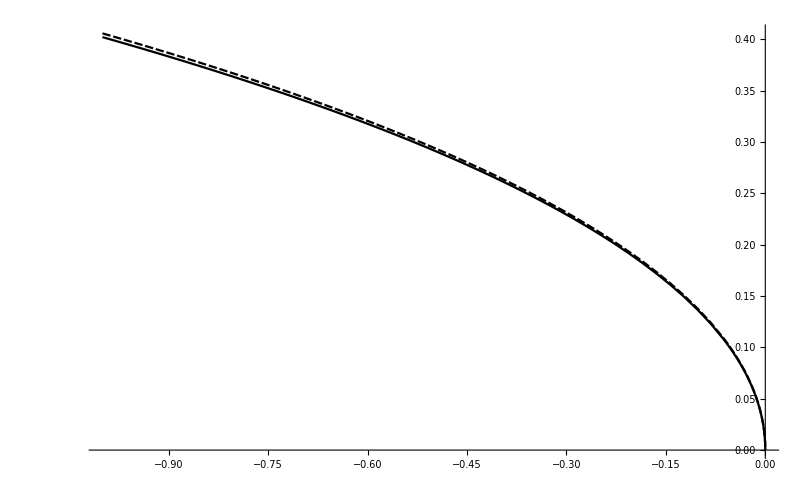

```mathematica
Plot[{Gammanewfun[ϵ],GammaC6[ϵ](*,GammaZero[ϵ]*)},{ϵ,-1.0,0}]
```

```mathematica
CalcTanEtaC6[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,gs,fs,fsp,gsp,k,tanη,αfun,phaseint,α,αp},
αfun = NDSolveValue[{α''[r] + ksqrC6[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1C6[Ε,l,r,rx],α'[rx] == BC2C6[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs =g[l,k,r];
gsp=dgdr[l,k,r];
tanη=(fs f0p-f0 fsp)/(gs f0p-f0 gsp)/.r->rf;
Return[tanη]
]
```

```mathematica
EtaTableC6=Table[{EGrid[[ii]],ArcTan[CalcTanEtaC6[ltest,rx,rf,r,EGrid[[ii]],ϕLi6[[1]]]]},{ii,1,Length[EGrid]}];
```

```mathematica
EtaTableC6new=EtaTableC6;
For[i=1,i<Length[EtaTable],i++,
If[(EtaTableC6[[i+1,2]]-EtaTableC6[[i,2]]>1.2),Print[i];
EtaTableC6new[[i+1;;Length[EtaTableC6],2]]=EtaTableC6new[[i+1;;Length[EtaTableC6],2]]-π,EtaTableC6new[[i+1;;Length[EtaTableC6],2]]=EtaTableC6new[[i+1;;Length[EtaTableC6],2]]]
]
```

216

482

```mathematica
EtaC6fun=Interpolation[EtaTableC6new,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Fit[EtaTableC6new,{ϵ^(1/2),ϵ,ϵ^(3/2),ϵ^2},ϵ]
```

```mathematica
EtaC6[ϵ_]:=-0.49977446657782576 √ϵ-0.03264396527849022 ϵ+0.006237423236577472 ϵ^(3/2)-0.00029131832549427963 ϵ^2
```

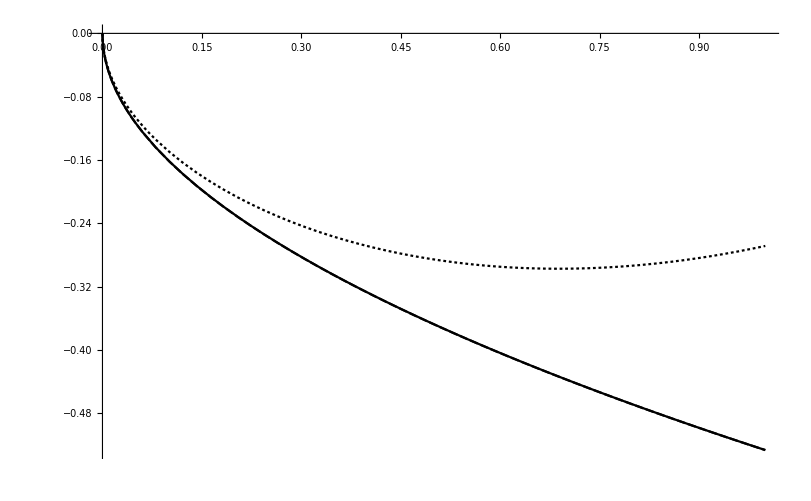

```mathematica
Plot[{Etafunnew[ϵ],EtaC6[ϵ],etazerofun[ϵ]},{ϵ,0,1.0}]
```

```mathematica
CalcAC6[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,fs,fsp,gs,gsp,k,A,αfun,phaseint,α,αp,tanη,Wfsf0,Wgsf0,Wfsg0,Wgsg0},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqrC6[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1C6[Ε,l,r,rx],α'[rx] == BC2C6[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,rf];
fsp=dfdr[l,k,rf];
gs=g[l,k,rf];
gsp=dgdr[l,k,rf];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
A=-((Wfsg0 -tanη Wgsg0)/(Wgsf0+tanη Wfsf0));
Return[A]
]
```

```mathematica
AC6Table=Table[{EGrid[[ii]],CalcAC6[ltest,rx,rf,r,EGrid[[ii]],ϕLi6[[1]]]},{ii,1,Length[EGrid]}];
```

```mathematica
AOneHalfC6Table = Table[{AC6Table[[ii,1]],-√(AC6Table[[ii,2]])},{ii,1,Length[AC6Table]}];
Fit[AOneHalfC6Table,{ϵ^(1/4),ϵ^(1/2),ϵ^(3/4),ϵ},ϵ]
```

```mathematica
AOneHalfC6[ϵ_]:=-0.7106525882422334 ϵ^(1/4)-0.013464033995034612 √ϵ+0.10043673238543206 ϵ^(3/4)-0.01805233552782764 ϵ
```

```mathematica
AC6fun = Interpolation[AC6Table,InterpolationOrder->1]
```

InterpolatingFunction[…]

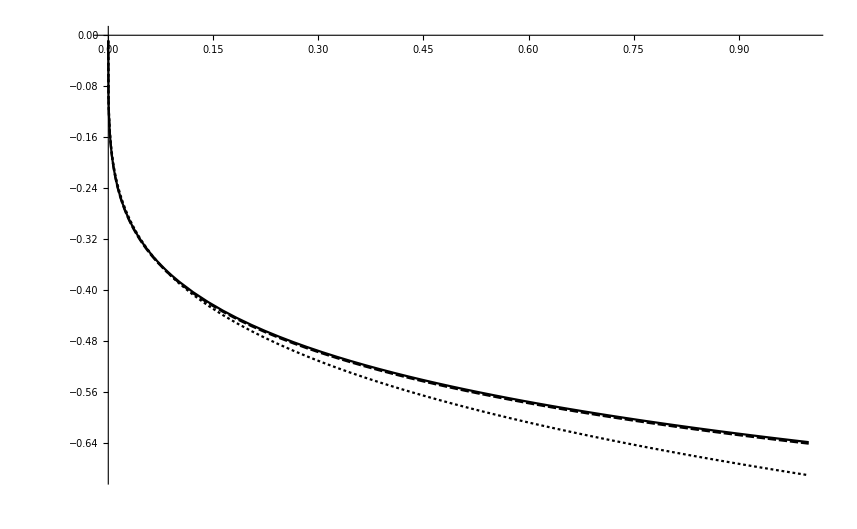

```mathematica
Plot[{AOneHalfnew[ϵ],AOneHalfC6[ϵ],AOneHalfzero[ϵ]},{ϵ,0,1.0}]
```

```mathematica
CalcGC6[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,k,tanη,G,fs,fsp,gs,gsp,αfun,phaseint,Wfsf0,Wgsf0,Wfsg0,Wgsg0,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqrC6[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1C6[Ε,l,r,rx],α'[rx] == BC2C6[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[ Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs=g[l,k,r];
gsp=dgdr[l,k,r];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
G=-(Wfsg0*Wfsf0+Wgsg0*Wgsf0)/(Wfsf0^2+Wgsf0^2)/.r->rf;
(*G =-((g0 gsp-g0p gs)+tanη(g0 fsp-g0p fs))/((f0 gsp - f0p gs)+tanη (f0 fsp - f0p fs))/.r->rf;*)
Return[G]
]
```

```mathematica
GC6Table=Table[{EGrid[[ii]],CalcGC6[ltest,rx,rf,r,EGrid[[ii]],ϕLi6[[1]]]},{ii,1,Length[EGrid]}];
```

```mathematica
GC6fun =Interpolation[GTable,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Fit[GC6Table[[1;;100]],{ϵ,ϵ^2,ϵ^3,ϵ^4},ϵ]
```

```mathematica
GC6[ϵ_]:=0.10302080839084801 ϵ-0.07389066572768314 ϵ^2+0.05309800584644725 ϵ^3-0.020610002565675762 ϵ^4
```

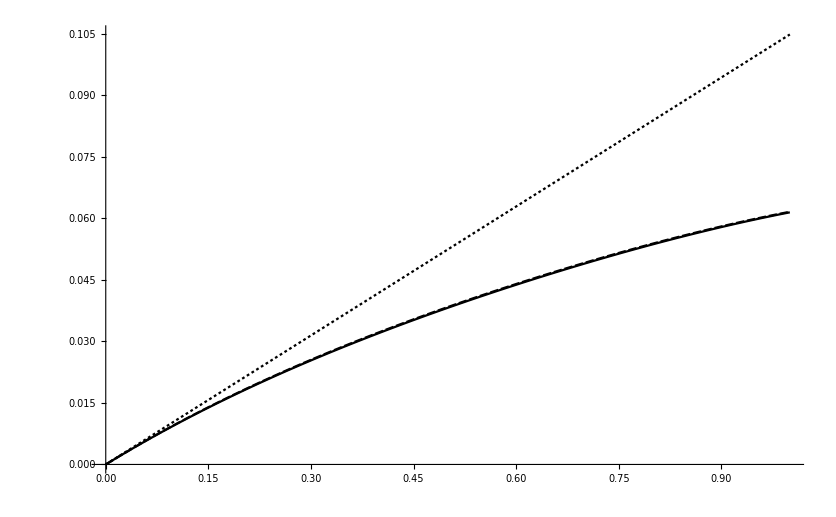

```mathematica
Plot[{Gnewfun[ϵ],GC6[ϵ],Gzero[ϵ]},{ϵ,0,1.0}]
```

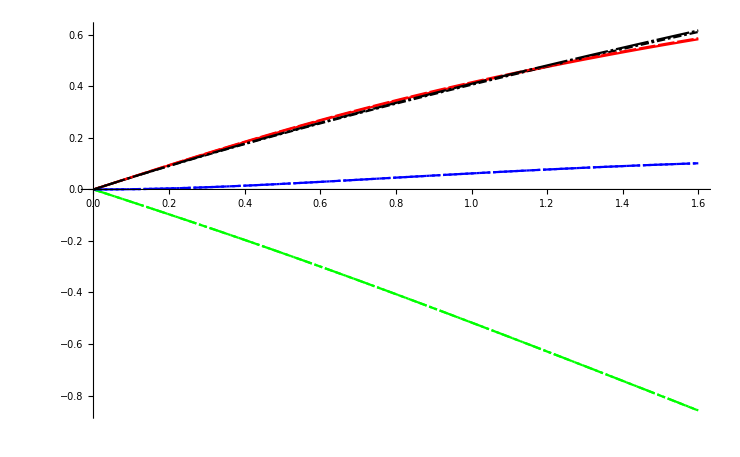

```mathematica
Plot[{Afun[κ^2],Etafun[κ^2],Gfun[κ^2],Gammafun[-κ^2],(*(AOneHalfzero[κ^2])^2,etazerofun[κ^2],Gzero[κ^2],GammaZero[-κ^2],*)AC6fun[κ^2],EtaC6fun[κ^2],GC6fun[κ^2],GammaC6fun[-κ^2]},{κ,0,1.6},PlotStyle->{Red,Green,Blue,Black,Red,Green,Blue,Black,Red,Green,Blue,Black}]
```